```mathematica
$MinPrecision=50;
```

```mathematica
G=1/((3*10^5)^2);
ϵ="e";μ="μ";τ="τ";

Subscript[f, π]=130;
Subscript[V, ud]=0.974;
Subscript[M, ϵ]=0.511; Subscript[M, μ]=105; Subscript[M, τ]=1777;Subscript[M, π0]=135;Subscript[M, π]=139.5;
γ[m_]:=(G^2 m^5)/(192 π^3);
Γννν[m_]:=γ[m](Subscript[θ, ϵ]^2+Subscript[θ, μ]^2+Subscript[θ, τ]^2);
Γllν[m_,α_,α_]:=Return[0];
Γllν[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(1-8 x^2+8 x^6-x^8-12 x^4 Log[x^2])/.x->Max[Subscript[M, α],Subscript[M, β]]/m;

w=0.2397;
Subscript[C, 1]=1/4(1-4w+8 w^2); Subscript[C, 3]=1/4(1+4w+8 w^2);
Subscript[C, 2]=1/2 w(2w-1); Subscript[C, 4]=1/2 w(2w+1);
L[x_]:=Log[(1-3 x^2-(1-x^2)√(1-4 x^2))/(x^2(1+√(1-4 x^2)))];
Γνll[m_,α_,β_]:=If[Subscript[M, α]+Subscript[M, β]<m,1,0]γ[m] Subscript[θ, α]^2(
If[α≠β,Subscript[C, 1],Subscript[C, 3]]((1-14 x^2-2 x^4-12 x^6)√(1-4 x^2)+12 x^4(x^4-1)L[x])+
4If[α≠β,Subscript[C, 2],Subscript[C, 4]](x^2(2+10 x^2-12 x^4)√(1-4 x^2)+6 x^4(1-2 x^2+2 x^4)L[x])
)/.x->SetAccuracy[Subscript[M, β]/m,100];
Γπν[m_,α_]:=If[Subscript[M, π0]<m,1,0] Subscript[θ, α]^2/(32π)G^2 Subscript[f, π]^2 m^3(1-Subscript[M, π0]^2/m^2)^2;
Γπl[m_,mH_,α_]:=If[mH+Subscript[M, α]<m,1,0] Subscript[θ, α]^2/(16π)G^2 Subscript[V, ud]^2 Subscript[f, π]^2 m^3((1-Subscript[M, α]^2/m^2)^2-mH^2/m^2(1+Subscript[M, α]^2/m^2))√((1-(mH-Subscript[M, α])^2/m^2)(1-(mH+Subscript[M, α])^2/m^2));
ΓHν[m_,mH_,α_]:=If[mH<m,1,0] Subscript[θ, α]^2/(32π)G^2 Subscript[f, π]^2 m^3(1-mH^2/m^2)^2;
```

```mathematica
Γ[m_]:=2Re[
Γννν[m]+(
Total[Γllν[m,#⟦1⟧,#⟦2⟧]+Γνll[m,#⟦1⟧,#⟦2⟧]&/@Tuples[{ϵ,μ,τ},2]]
)+(
Total[Γπν[m,#]+Γπl[m,Subscript[M, π],#]&/@{ϵ,μ,τ}]
)
];
ΓDirac[m_]:=Γ[m]/2;
ΓDolgov[m_]:=((1+(w-1/2)^2+w^2)G^2 m^5 Sin[2 Subscript[θ, τ]]^2/4)/(192 π^3);
```

```mathematica
MEVtoSEC[mev_]:=(6.582 10^-22)/mev;
```

```mathematica
θs[z_:1]:={Subscript[θ, ϵ]->z/(√m)√(1.3 10^-8),Subscript[θ, μ]->z/(√m)√(3.8 10^-7),Subscript[θ, τ]->z/(√m)√(3.2 10^-7)}
(*θs[z_:1]:={Subscript[θ, ϵ]->0,Subscript[θ, μ]->0,Subscript[θ, τ]->0.0486}*)
```

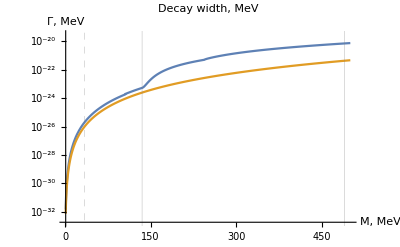
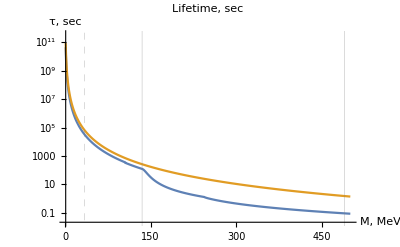

33339.5

```mathematica
Row[{LogPlot[{ΓDirac[m]/.θs[],ΓDolgov[m]/.θs[]},{m,1,500},PlotRange->All,PlotLabel->"Decay width, MeV",AxesLabel->{"M, MeV","Γ, MeV"},PlotPoints->150,ImageSize->400,GridLines->{{{33.9,Dashed},135,490},{}}],
LogPlot[{MEVtoSEC[ΓDirac[m]/.θs[]],MEVtoSEC[ΓDolgov[m]/.θs[]]},{m,1,500},PlotRange->All,PlotLabel->"Lifetime, sec",AxesLabel->{"M, MeV","τ, sec"},PlotPoints->150,ImageSize->400,GridLines->{{{33.9,Dashed},135,490},{}}]
}]
MEVtoSEC[ΓDirac[m]/.θs[]]/.m->33.9
```

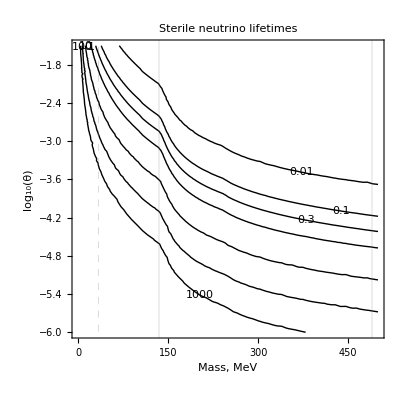

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min];
Show[
ContourPlot[
(MEVtoSEC[Γ[m]]/.θs[10^(y+4)]),
{m,00,500},{y,-6,-1.5},
Contours->{0.01,0.1,0.3,1,10,100,1000},
ContourLabels->All,
ColorFunctionScaling->False,ContourShading->None
],GridLines->{{{33.9,Dashed},135,490},{}},
PlotLabel->"Sterile neutrino lifetimes",
FrameLabel->{"Mass, MeV","log_10(θ)"}
]
```

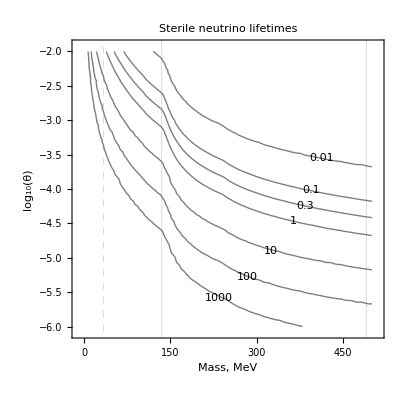

```mathematica
Computeθ[m_,t_]:=x/.FindRoot[(MEVtoSEC[ΓDirac[m]]/.{Subscript[θ, ϵ]->x,Subscript[θ, μ]->0,Subscript[θ, τ]->0})==t,{x,10^-10}]
Computeθτ[m_,t_]:=x/.FindRoot[(MEVtoSEC[ΓDirac[m]]/.{Subscript[θ, ϵ]->0,Subscript[θ, μ]->0,Subscript[θ, τ]->x})==t,{x,10^-10}]

(*data = {
{20,0.44945},{20,1.50822},
{40,0.117643},{40,0.250714},
{60,0.0670581},{60,0.155819},
{80,0.0517349},{80,0.125525},
{100,0.0495457},{100,0.105589},
{120,0.048486},{120,0.0947709}
};

params={#⟦1⟧,Computeθ[#⟦1⟧,#⟦2⟧],#⟦2⟧}&/@data;
params//MatrixForm
StringJoin["python tests/paper_oscillations --mass "<>ToString[N[#⟦1⟧]]<>" --tau "<>ToString[N[#⟦3⟧]]<>" --theta "<>ToString[N[#⟦2⟧]]<>" --Tdec "<>ToString[1.5 N[Tdec[#⟦1⟧,#⟦2⟧]]]<>"\n"&/@params]*)
```

```mathematica
Tdec[m_,θ_]:=Block[{γ,g,Mpl,T},(
g[T_]:=Piecewise[{{7.25,T≤0.5},{10.75,T≤105},{14.25,T≤170},{61.75,T≤ 1000},{75,True}},T];
Mpl[T_]:=(1.22 10^22)/(1.66 √g[T]);
γ[T_]:=G^2 θ^2 Mpl[T];
Td=T/.FindRoot[m^2==1/(γ[T]T),{T,100}];
If[Td>m,Td=T/.FindRoot[T^3 γ[T] ==1,{T,100}]];
Return[N[Td]];
)];
Tdec[0,1]
Tdec[100,10^-4]
Tdec[100,10^-2]
```

N::precsm: Requested precision 18.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1.53454

N::precsm: Requested precision 18.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

953.2

N::precsm: Requested precision 18.9546 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

3.61358